```mathematica
v0={0,1,2,3}

u0={413,100,90,421}
```

{0,1,2,3}

{413,100,90,421}

```mathematica
w=Table[{v0[[i]],u0[[i]]/(2*Sqrt[2]*1024.)},{i,4}]
```

{{0,0.142595},{1,0.0345267},{2,0.031074},{3,0.145357}}

```mathematica
f[x_]=Fit[w,Table[x^i,{i,0,4}],x]
```

0.142595-0.149471 x+0.0337716 x^2+0.00871919 x^3-0.00108875 x^4

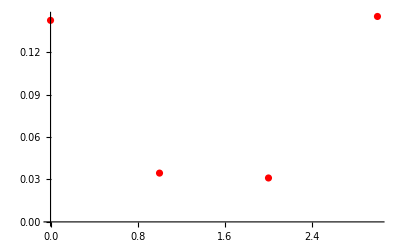

```mathematica
g1=ListPlot[w,PlotStyle->Red, ImageSize->Full]
```

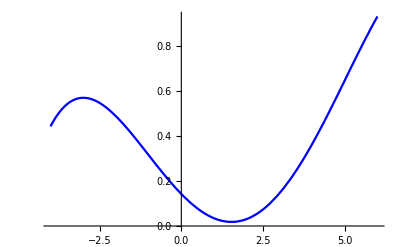

```mathematica
g2=Plot[f[x],{x,-4,6},PlotStyle->Blue, ImageSize->Full,PlotRange->All]
```

```mathematica
f[1.5]
```

0.0182909

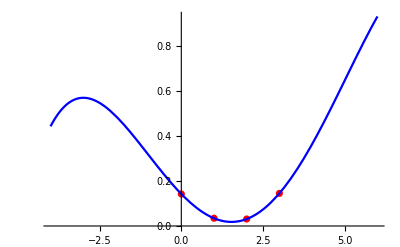

```mathematica
Show[{g1,g2},PlotRange->All]
```